```mathematica
<<VilCretas`
```

VilCretas está disponible.

```mathematica
RelacionComposicion[R1_,R2_]:=Module[{Composicion={},i,j},For[i=1,i<=Length[R2],For[j=1,j<=Length[R1],If[R2[[i,2]]==R1[[j,1]],Composicion=Append[Composicion,{R2[[i,1]],R1[[j,2]]}]];j++];
i++];DeleteDuplicates[Composicion]]
```

# Ejercicio 1 -Graphics-

```mathematica
A={14,18,35,41,47};
R1={{14,18},{14,41},{18,18},{35,14},{35,18},{35,35},{41,35},{47,14}};
R2={{14,18},{14,41},{14,47},{18,18},{18,35},{18,47},{41,18},{47,35}};
MR1 = MatrizRelBin[R1,A,A][[1]];
MR2 = MatrizRelBin[R2,A,A][[1]];
R = InterseccionBooleana[UnionBooleana[Transpose[MR1],MR2,lista->True], ComplementoBooleano[InterseccionBooleana[MR1,MR2,lista->True],lista->True],lista->True]//MatrixForm
R = R[[1]];
RelBinMatriz[R,A,A]
```

(0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{{14,35},{14,47},{18,14},{18,35},{18,47},{35,35},{35,41},{41,14},{41,18},{47,35}}

```mathematica
RA = Intersection[Union[Reverse/@R1,R2],Complement[PC[A,A],Intersection[R1,R2]]]
```

{{14,35},{14,47},{18,14},{18,35},{18,47},{35,35},{35,41},{41,14},{41,18},{47,35}}

```mathematica
MatrizRelBin[RA,A,A]
```

(0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

```mathematica
({{0, 0, 1, 0, 1}, {1, 0, 1, 0, 1}, {0, 0, 1, 1, 0}, {1, 1, 0, 0, 0}, {0, 0, 1, 0, 0}}) ==({{0, 0, 1, 0, 1}, {1, 0, 1, 0, 1}, {0, 0, 1, 1, 0}, {1, 1, 0, 0, 0}, {0, 0, 1, 0, 0}})
```

True

# Ejercicio 2 -Graphics-

```mathematica
Clear[A]
Clear[R1,R2,MR1,MR2,R,RA]
```

```mathematica
A = {100,8,55,34,81,1,39,87,53,16};
B= {13,62,21,66,44,88,93,95,80,16};
H = {22,64,5,18,95,72,52,44,98,10};
R1 = {{8,88},{100,80},{53,80},{100,44},{87,93},{53,16},{8,93},{87,13},{1,62},{100,93}};
R2 = {{16,22},{95,98},{88,10},{66,5},{80,72},{21,22},{88,44},{62,72},{80,22},{66,72}};
RelacionComposicion[R2,R1]
MR1 =MatrizRelBin[R1,A,B][[1]];
MR2 =MatrizRelBin[R2,B,H][[1]];
MR = RelBinMatriz[ProductoBooleano[MR1,MR2,lista->True],A,H]
```

{{8,10},{8,44},{100,72},{100,22},{53,72},{53,22},{1,72}}

{{1,72},{8,10},{8,44},{53,22},{53,72},{100,22},{100,72}}

```mathematica
L = {{1,72},{8,10},{8,44},{53,22},{53,72},{100,22},{100,72}};
S = {{8,10},{8,44},{100,72},{100,22},{53,72},{53,22},{1,72}};
V = {{100,22},{87,95},{1,72},{39,64},{53,22},{34,10}};
```

```mathematica
Table[i->ElementRelBinQ[L,i],{i, V}]
Table[i->ElementRelBinQ[S,i],{i,V}]
```

{{100,22}→True,{87,95}→False,{1,72}→True,{39,64}→False,{53,22}→True,{34,10}→False}

{{100,22}→True,{87,95}→False,{1,72}→True,{39,64}→False,{53,22}→True,{34,10}→False}

# Ejercicio 3 -Graphics-

```mathematica
A={56,5,52,35,72,21,36};
MR = ({{1, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0}})
R = RelBinMatriz[MR,A,A]
ClasificacionRelBin[R,A]
```

{{1,0,0,1,0,1,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{1,0,0,1,0,1,0},{0,0,0,0,0,0,0},{1,0,0,1,0,1,0},{0,0,0,0,0,0,0}}

{{21,21},{21,35},{21,56},{35,21},{35,35},{35,56},{56,21},{56,35},{56,56}}

{False,True,False,True}

# Ejercicio 4

```mathematica
A ={2,7,9,10,11,12,14,17,18,20,23,25,26,27,29,36,39,41,43,48};
B ={3,4,6,7,11,16,20,23,25,26,27,29,31,36,40,41,47,48,49,50};
R = RelBin["Mod[a+b,2]!=0",A,B]
j = RelBin["OddQ[a+b]==True",A,B]
ElementRelBinQ[j,{23,36}]
Length[j]
ElementRelBinQ[R,{23,36}]
Length[R]
```

{{2,3},{2,7},{2,11},{2,23},{2,25},{2,27},{2,29},{2,31},{2,41},{2,47},{2,49},{7,4},{7,6},{7,16},{7,20},{7,26},{7,36},{7,40},{7,48},{7,50},{9,4},{9,6},{9,16},{9,20},{9,26},{9,36},{9,40},{9,48},{9,50},{10,3},{10,7},{10,11},{10,23},{10,25},{10,27},{10,29},{10,31},{10,41},{10,47},{10,49},{11,4},{11,6},{11,16},{11,20},{11,26},{11,36},{11,40},{11,48},{11,50},{12,3},{12,7},{12,11},{12,23},{12,25},{12,27},{12,29},{12,31},{12,41},{12,47},{12,49},{14,3},{14,7},{14,11},{14,23},{14,25},{14,27},{14,29},{14,31},{14,41},{14,47},{14,49},{17,4},{17,6},{17,16},{17,20},{17,26},{17,36},{17,40},{17,48},{17,50},{18,3},{18,7},{18,11},{18,23},{18,25},{18,27},{18,29},{18,31},{18,41},{18,47},{18,49},{20,3},{20,7},{20,11},{20,23},{20,25},{20,27},{20,29},{20,31},{20,41},{20,47},{20,49},{23,4},{23,6},{23,16},{23,20},{23,26},{23,36},{23,40},{23,48},{23,50},{25,4},{25,6},{25,16},{25,20},{25,26},{25,36},{25,40},{25,48},{25,50},{26,3},{26,7},{26,11},{26,23},{26,25},{26,27},{26,29},{26,31},{26,41},{26,47},{26,49},{27,4},{27,6},{27,16},{27,20},{27,26},{27,36},{27,40},{27,48},{27,50},{29,4},{29,6},{29,16},{29,20},{29,26},{29,36},{29,40},{29,48},{29,50},{36,3},{36,7},{36,11},{36,23},{36,25},{36,27},{36,29},{36,31},{36,41},{36,47},{36,49},{39,4},{39,6},{39,16},{39,20},{39,26},{39,36},{39,40},{39,48},{39,50},{41,4},{41,6},{41,16},{41,20},{41,26},{41,36},{41,40},{41,48},{41,50},{43,4},{43,6},{43,16},{43,20},{43,26},{43,36},{43,40},{43,48},{43,50},{48,3},{48,7},{48,11},{48,23},{48,25},{48,27},{48,29},{48,31},{48,41},{48,47},{48,49}}

{{2,3},{2,7},{2,11},{2,23},{2,25},{2,27},{2,29},{2,31},{2,41},{2,47},{2,49},{7,4},{7,6},{7,16},{7,20},{7,26},{7,36},{7,40},{7,48},{7,50},{9,4},{9,6},{9,16},{9,20},{9,26},{9,36},{9,40},{9,48},{9,50},{10,3},{10,7},{10,11},{10,23},{10,25},{10,27},{10,29},{10,31},{10,41},{10,47},{10,49},{11,4},{11,6},{11,16},{11,20},{11,26},{11,36},{11,40},{11,48},{11,50},{12,3},{12,7},{12,11},{12,23},{12,25},{12,27},{12,29},{12,31},{12,41},{12,47},{12,49},{14,3},{14,7},{14,11},{14,23},{14,25},{14,27},{14,29},{14,31},{14,41},{14,47},{14,49},{17,4},{17,6},{17,16},{17,20},{17,26},{17,36},{17,40},{17,48},{17,50},{18,3},{18,7},{18,11},{18,23},{18,25},{18,27},{18,29},{18,31},{18,41},{18,47},{18,49},{20,3},{20,7},{20,11},{20,23},{20,25},{20,27},{20,29},{20,31},{20,41},{20,47},{20,49},{23,4},{23,6},{23,16},{23,20},{23,26},{23,36},{23,40},{23,48},{23,50},{25,4},{25,6},{25,16},{25,20},{25,26},{25,36},{25,40},{25,48},{25,50},{26,3},{26,7},{26,11},{26,23},{26,25},{26,27},{26,29},{26,31},{26,41},{26,47},{26,49},{27,4},{27,6},{27,16},{27,20},{27,26},{27,36},{27,40},{27,48},{27,50},{29,4},{29,6},{29,16},{29,20},{29,26},{29,36},{29,40},{29,48},{29,50},{36,3},{36,7},{36,11},{36,23},{36,25},{36,27},{36,29},{36,31},{36,41},{36,47},{36,49},{39,4},{39,6},{39,16},{39,20},{39,26},{39,36},{39,40},{39,48},{39,50},{41,4},{41,6},{41,16},{41,20},{41,26},{41,36},{41,40},{41,48},{41,50},{43,4},{43,6},{43,16},{43,20},{43,26},{43,36},{43,40},{43,48},{43,50},{48,3},{48,7},{48,11},{48,23},{48,25},{48,27},{48,29},{48,31},{48,41},{48,47},{48,49}}

True

198

True

198

# Ejercicio 5 -Graphics-

{{25,44},{25,64},{25,95},{44,64},{95,64}}

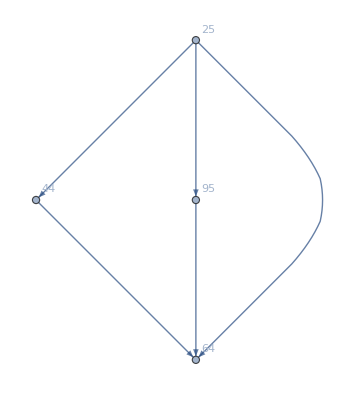

```mathematica
R = {{25,44},{25,64},{25,95},{44,64},{95,64}}
Grafo[R,dirigido->True]
```

```mathematica
L = {{{25,44},{25,64},{25,95},{44,64},{95,64}},{{25,44},{25,64},{25,25},{44,64},{95,64}},{{44,25},{25,64},{25,95},{44,64},{95,64}},{{25,44},{25,64},{25,95},{44,64},{64,95}},{{25,44},{25,64},{95,25},{44,64},{95,64}}}
```

{{{25,44},{25,64},{25,95},{44,64},{95,64}},{{25,44},{25,64},{25,25},{44,64},{95,64}},{{44,25},{25,64},{25,95},{44,64},{95,64}},{{25,44},{25,64},{25,95},{44,64},{64,95}},{{25,44},{25,64},{95,25},{44,64},{95,64}}}

```mathematica
Table[R == i,{i,L}]
```

{True,False,False,False,False}

```mathematica
R == L[[1]]
R == {{25,44},{25,64},{25,95},{44,64},{95,64}}
```

True

True

# Ejercicio 6

```mathematica
A = Range[-5,1000,5];
B = Range[5,1000,5];
Length[PC[A,B]]
```

40400

# Ejercicio 7 -Graphics-

```mathematica
A = Range[1,100,3];
R = RelBin["a>b&&Mod[a-b,20]==0",A,A]
Dom = DominioRelBin[R]
Length[Dom]
```

{{61,1},{64,4},{67,7},{70,10},{73,13},{76,16},{79,19},{82,22},{85,25},{88,28},{91,31},{94,34},{97,37},{100,40}}

{61,64,67,70,73,76,79,82,85,88,91,94,97,100}

14